```mathematica
CircleLayout[n_]:=Table[{Cos[(2π/n )(n-i+1)+Pi/2],Sin[(2π/n )(i-1)+Pi/2]},{i,n}]
```

```mathematica
GenAll[n_]:=Block[
{nodes},
nodes=Table[{i},{i,n}];
GenAllFromList[nodes]
]
```

```mathematica
PairWiseCombine[list_]:=Block[
{l=Length[list], sets,result={},temp,newItem},
sets=Subsets[Range[l],{2}];
result=Table[
temp=Table[k,{k,list}];
newItem=Sort[{s[[1]],s[[2]]}];
temp=Drop[temp,{newItem[[2]]}];
temp=Drop[temp,{newItem[[1]]}];
temp=Append[temp,Sort[Join[list[[newItem[[1]]]],list[[newItem[[2]]]]]]];
temp=Sort[temp];
temp
,
{s,sets}
];
result
]
```

```mathematica
MyCircle2[vertices_,length_]:=Block[{pos=N[ CircleLayout[length]], midPoint,temp,i,div},
midPoint=Mean[Table[pos[[v]],{v,vertices}]];
div=Sqrt[midPoint[[1]]^2+midPoint[[2]]^2];
If[True,
midPoint=pos[[vertices[[1]]]],
midPoint=midPoint/div
];
N[midPoint]
]
```

```mathematica
MyCircle[vertices_,length_]:=Block[{pos=N[ CircleLayout[length]], sum={0,0}},
Map[MyCircle2[#,length]&,vertices]
]
```

```mathematica
AllGraphs[list_]:=Block[
{l=Length[list],longLength=Total[Map[Length[#]&,list]], sets,result={},temp,g, mat, element, realResult},
(* subsets are the vertices that we will connect *)
sets=Subsets[Subsets[Range[l],{2}]];
result=Table[
(* create a matrix that is "not connected" *)
mat=Table[0,{i,longLength},{j,longLength}];
(* Mark everything within one bucket as "2" *)
Table[
Table[mat[[i,j]]=2;mat[[j,i]]=2,{i,list[[bucket]]},{j,list[[bucket]]}],
{bucket,l}
];

(* Mark everything for linked edges as "1" *)
Table[
Table[mat[[i,j]]=1;mat[[j,i]]=1,{i,list[[s2[[1]]]]},{j,list[[s2[[2]]]]}],
{s2,s}
];
g=Graph[Range[l],
Table[
s2[[1]]<->s2[[2]]
,{s2,s}
],
VertexLabels->Table[i->StringRiffle[ list[[i]],","],{i,l}],
VertexCoordinates->MyCircle[list,longLength],
VertexStyle->Red,
VertexSize->0.1,
EdgeStyle->{Thickness[0.02],Darker[Green]},
ImageSize->{50,50}
];
element=Association[];
element["signature"]=GraphMatrixSignature[mat];
element["matrix"]=mat;
element["graph"]=g;
element["vertexsets"]=list;
element["vertices"]=Range[l];
element["edges"]=s;
element["relations"]={};
element["links"]={};
element
,
{s,sets}
];
realResult=Association[];
Table[
realResult[el["signature"]]=el,
{el,result}
];
realResult
]
```

```mathematica
GenAllFromList[{{4},{6},{1,3},{2,5}}]//First
```

{{4},{6},{1,3},{2,5}}

```mathematica
GenAllFromList[list_]:=Block[
{nodes,result},

result=AllGraphs[list];
If[Length[list]>1,
Table[
Table[
result[el["signature"]]=el,
{el,GenAllFromList[v]}
]
,
{v,PairWiseCombine[list]}
]
];
result
]
```

```mathematica
GraphMatrixSignature[matrix_]:=Block[{l=Length[matrix]},
FromDigits[
Flatten[
Table[Table[matrix[[i,j]],{j,i+1,l}],{i,1,l}]
],3]
]
```

```mathematica
GraphMatrixSignature2[matrix_,indexSet1_,indexSet2_, newValue_]:=Block[
{temp=matrix, result},
Table[
temp[[i2,j2]]=newValue;
temp[[j2,i2]]=newValue;
,{i2,indexSet1},{j2,indexSet2}];

Table[
temp[[i,i]]=2;
,{i,Length[temp]}];
result=GraphMatrixSignature[temp];
Print["---->", result, temp];
result
]
```

```mathematica
CompressGraph[full_,vertices_]:=Block[
{x,y,l=Length[vertices],a,b},
Table[
a=vertices[[i,1]];
b=vertices[[j,1]];
full[[a,b]]
,{i,l},{j,l}
]
]
```

```mathematica
UnCompressGraph[small_,vertices_]:=Block[
{x,l=Total[Map[Length[#]&,vertices]],a,b,result,l2=Length[vertices]},
result=Table[0,{i,l},{j,l}];
Table[
a=vertices[[i]];
b=vertices[[j]];
x=small[[i,j]];
Table[
result[[a1,b1]]=x,{a1,a},{b1,b}
]
,{i,l2},{j,l2}
];
result
]
```

```mathematica
GraphMatrixSignature2[currentCompressed_,i_,j_,value_,currentVertexSets_]:=Block[
{uncomp=currentCompressed,sig,mat,l=Length[currentCompressed],m},
(* if the value is 2 then we run over the columns i and j and assign the maximum of both columns to each.
  This makes sure that connected stays connected and merged stays merged *)
If[value==2,
Table[
m=Max[uncomp[[i,a]],uncomp[[j,a]]];
uncomp[[j,a]]=m;
uncomp[[i,a]]=m;

uncomp[[a,j]]=m;
uncomp[[a,i]]=m
,{a,l}];

(*Print["uncomp",i, "  ", j, "  ",sig, "  ",MatrixForm[uncomp]];*)

];
uncomp[[i,j]]=value;
uncomp[[j,i]]=value;
mat=UnCompressGraph[uncomp,currentVertexSets];
sig=GraphMatrixSignature[mat];
(*Print["uncompressed",i, "  ", j, "  ",sig, "  ",MatrixForm[currentCompressed]-> MatrixForm[mat]];*)
sig
]
```

```mathematica
CompleteRelations[assocs_]:=Block[
{current, currentGraph, currentID,currentMatrix,currentVertexSets, currentCompressed,one,two, relations={}, links,l, newAssocs=Association[],keep, count=0},
Monitor[
Table[
count++;
current=assocs[key];
currentGraph=current["graph"];
currentID=current["signature"];
currentMatrix=current["matrix"];
currentVertexSets=current["vertexsets"];
currentCompressed=CompressGraph[currentMatrix,currentVertexSets];
keep=currentCompressed;
l=Length[currentCompressed];
links={};
relations={};

Table[
currentCompressed=keep;
If[currentCompressed[[i,j]]==2,
(* current is contracted of one and two *)
one=GraphMatrixSignature2[currentCompressed,i,j,1,currentVertexSets];
two=GraphMatrixSignature2[currentCompressed,i,j,0,currentVertexSets];


If[KeyExistsQ[assocs,two]&&KeyExistsQ[assocs,one],
AppendTo[relations,Symbol["x"<>ToString[key]]== Symbol["x"<>ToString[two]]-Symbol["x"<>ToString[one]]]
,
Print[one, "   ",KeyExistsQ[assocs,one],"  ", two, "   ",KeyExistsQ[assocs,two], "  ", currentMatrix//MatrixForm, "   ", keep//MatrixForm, "   ",i , "   ", j, "  3333 ", currentVertexSets];
Interrupt[]
]
,
If[currentCompressed[[i,j]]==1,
(* current is connected of one and two *)
one=GraphMatrixSignature2[currentCompressed,i,j,2,currentVertexSets];
two=GraphMatrixSignature2[currentCompressed,i,j,0,currentVertexSets];


If[KeyExistsQ[assocs,two]&&KeyExistsQ[assocs,one],
AppendTo[relations,Symbol["x"<>ToString[key]]== Symbol["x"<>ToString[two]]-Symbol["x"<>ToString[one]]]
,
Print[one, "   ",KeyExistsQ[assocs,one],"  ", two, "   ",KeyExistsQ[assocs,two], "  ", currentMatrix//MatrixForm, "   ", keep//MatrixForm, "   ",i , "   ", j, "  3333 ", currentVertexSets];
Interrupt[]
]
,
(* current is unconnected of one and two *)
one=GraphMatrixSignature2[currentCompressed,i,j,2,currentVertexSets];
two=GraphMatrixSignature2[currentCompressed,i,j,1,currentVertexSets];
AppendTo[links,one];
AppendTo[links,two];

If[KeyExistsQ[assocs,two]&&KeyExistsQ[assocs,one],
AppendTo[relations,Symbol["x"<>ToString[key]]== Symbol["x"<>ToString[two]]+Symbol["x"<>ToString[one]]]
,
Print[one, "   ",KeyExistsQ[assocs,one],"  ", two, "   ",KeyExistsQ[assocs,two], "  ", currentMatrix//MatrixForm, "   ", keep//MatrixForm, "   ",i , "   ", j, "  3333 ", currentVertexSets];
Interrupt[]
]
]
]
,{i,1,l},{j,i+1,l}
];
current["relations"]=relations;
(*PrintTemporary[relations];*)
current["links"]=links;
newAssocs[key]=current
,
{key, Sort[Keys[assocs]]}
],
{count,key}];
newAssocs
]
```

```mathematica
SymbolComp[x_,y_]:=Block[{a,b,o,p},
a=StringTake[SymbolName[x],1];
b=StringTake[SymbolName[y],1];
If[a≠b,Return[a<b]];
o=FromDigits[StringPadLeft[StringDrop[SymbolName[x],1],3,"0"]];
p=FromDigits[StringPadLeft[StringDrop[SymbolName[y],1],3,"0"]];
Return[o<p]
]
TrueQ["c">"b"]
False
ExpComp[d1>0,d10>0]
False
LongSymbol[x_]:=Block[{comp, start,end},
comp=ToString[x];
start=StringTake[comp,1];
end=StringPadLeft[ StringDrop[comp,1],3,"0"];
start<>end
]
ExpComp[x_,y_]:=Block[{
varx=getAllVariables[x],
vary=getAllVariables[y],
o,p},
If[Length[varx]≠Length[vary],
Return [Length[varx]<Length[vary]]
];
varx=Sort[varx,SymbolComp];
vary=Sort[vary,SymbolComp];
o=StringJoin[Map[ LongSymbol,varx]];
p=StringJoin[Map[LongSymbol,vary]];
Order[o,p]>0
]
ExpressionToTable2[exp_]:=Block[
{vals=Sort[Monitor[Table[exp[[i]]//Simplify,{i,1,Length[exp]}],{i,Length[exp]}]]},
TableForm[Sort[vals,ExpComp],TableDirections->Column]
]
```

False

False

ExpComp[d1>0,d10>0]

False

```mathematica
ExpressionToTable[exp_]:=Block[
{vals=Sort[Monitor[Table[exp[[i]]//Simplify,{i,1,Length[exp]}],{i,Length[exp]}]]},
TableForm[Sort[vals,ExpComp],TableDirections->Column]
]
```

```mathematica
OnlyOnex[exp_]:=Block[{
v=getAllVariables[exp]},
Length[Select[v,StringTake[ SymbolName[#],1]=="x"&]]==1
]
```

```mathematica
NotASingleX[exp_]:=Block[{
v=ListofVars[exp]//DeleteDuplicates},
Length[Select[v,StringTake[ SymbolName[#],1]=="x"&]]==0
]
```

```mathematica
OnlyTwox[exp_]:=Block[{
v=getAllVariables[exp]},
Length[Select[v,StringTake[ SymbolName[#],1]=="x"&]]==2
]
```

```mathematica
OnlyXVar[exp_]:=Block[{
v=getAllVariables[exp]},
First[Select[v,StringTake[ SymbolName[#],1]=="x"&]]
]
```

```mathematica
XVar[exp_]:=Block[{
v=getAllVariables[exp]},
Select[v,StringTake[ SymbolName[#],1]=="x"&]
]
```

```mathematica
GraphMatrixSignature[({{2,0,1,1},{0,2,0,0},{1,0,2,2},{1,0,2,2}})]
```

110

```mathematica
AllGraphs[{{1},{2},{3,4}}]//DeleteDuplicates
```

<|2→<|signature→2,matrix→{{2,0,0,0},{0,2,0,0},{0,0,2,2},{0,0,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{},relations→{},links→{}|>,245→<|signature→245,matrix→{{2,1,0,0},{1,2,0,0},{0,0,2,2},{0,0,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,2}},relations→{},links→{}|>,110→<|signature→110,matrix→{{2,0,1,1},{0,2,0,0},{1,0,2,2},{1,0,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,3}},relations→{},links→{}|>,14→<|signature→14,matrix→{{2,0,0,0},{0,2,1,1},{0,1,2,2},{0,1,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{2,3}},relations→{},links→{}|>,353→<|signature→353,matrix→{{2,1,1,1},{1,2,0,0},{1,0,2,2},{1,0,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,2},{1,3}},relations→{},links→{}|>,257→<|signature→257,matrix→{{2,1,0,0},{1,2,1,1},{0,1,2,2},{0,1,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,2},{2,3}},relations→{},links→{}|>,122→<|signature→122,matrix→{{2,0,1,1},{0,2,1,1},{1,1,2,2},{1,1,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,3},{2,3}},relations→{},links→{}|>,365→<|signature→365,matrix→{{2,1,1,1},{1,2,1,1},{1,1,2,2},{1,1,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,2},{1,3},{2,3}},relations→{},links→{}|>|>

```mathematica
headlist={Or,And,Equal,Unequal,Less,LessEqual,Greater,GreaterEqual,Inequality};

getAllVariables[f_?NumericQ]:=Sequence[]
getAllVariables[{}]:=Sequence[]
getAllVariables[t_]/;MemberQ[headlist,t]:=Sequence[]

getAllVariables[ll_List]:=Flatten[Union[Map[getAllVariables[#]&,ll]]]

getAllVariables[Derivative[n_Integer][f_][arg__]]:=getAllVariables[{arg}]

getAllVariables[f_Symbol[arg__]]:=Module[{fvars},If[MemberQ[Attributes[f],NumericFunction]||MemberQ[headlist,f],fvars=getAllVariables[{arg}],(*else*)fvars=f[arg]];
fvars]

getAllVariables[other_]:=other
```

```mathematica
ListofVars[exp_]:=With[{kk=getAllVariables[exp]},If[ListQ[kk],kk,{kk}]]
```

```mathematica
CosyPrint[key_]:=With[
{current=newAssoc[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{50,50}],"   ",
Graph[VertexList[current["graph"]],EdgeList[current["graph"]],GraphLayout->"TutteEmbedding",ImageSize->{50,50}],"   ",
Style[TableForm[Map[FullSimplify[#/.replaceMents/.α+β+γ+δ+ϵ-λ->α1+β1+γ1+δ1+ϵ1]&,
current["relations"]]],FontSize->12, FontFamily->"Consolas"], "   ",
MatrixForm[current["matrix"]]
}
],Style[
{If[KeyExistsQ[current,"colofour"],
current["signature"]->TraditionalForm[current["colofour"]/.replaceMents/.α+β+γ+δ+ϵ-λ->α1+β1+γ1+δ1+ϵ1],
current["signature"]
],ChromaticPolynomial[current["graph"],4]/24},Red]]]
]
```

```mathematica
CosyPrint2[key_]:=With[
{current=newAssoc[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{50,50}],"   ",
Graph[VertexList[current["graph"]],EdgeList[current["graph"]],GraphLayout->"TutteEmbedding",ImageSize->{50,50}],"   ",
Style[TableForm[Map[FullSimplify[#]&,
current["relations"]]],FontSize->12, FontFamily->"Consolas"], "   ",
MatrixForm[current["matrix"]]
}
],Style[
{current["signature"]->
If[KeyExistsQ[current,"comp"],current["comp"],GreaterEqual][TraditionalForm[current["colofour"]/.replaceMents/.α+β+γ+δ+ϵ-λ->α1+β1+γ1+δ1+ϵ1]
,0],If[KeyExistsQ[current,"compwhy"],current["compwhy"],""]},Red]]]
]
```

```mathematica
SymbolComp2[x_,y_]:=Block[{n1=SymbolName[x],n2=SymbolName[y],a,b,h1,h2},
h1=StringTake[n1,1];
h2=StringTake[n2,1];
If[h1≠h2,
Return[h1<h2]
];
a=SymbolToKey[n1];
b=SymbolToKey[n2];
a<b
]
```

```mathematica
CoeffVector[v_]:=Table[Coefficient[ (v/.replaceMents)*24,v,1],{v,Sort[myVars,SymbolComp2]}]
```

```mathematica
CosyPrint3[key_]:=With[
{current=newAssoc[key]},
Column[
{
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{50,50}],"   ",
Graph[VertexList[current["graph"]],EdgeList[current["graph"]],GraphLayout->"TutteEmbedding",ImageSize->{50,50}],"   ",
Style[MatrixForm[Map[First,current["colortable3"]],TableHeadings->{Map[#[[1]]<->#[[2]]&,Subsets[Range[5],{2}]], "="}, TableSpacing->{2, 3}],FontSize->10, FontFamily->"Consolas"]
}
],Style[
{current["signature"]->
If[KeyExistsQ[current,"comp"],current["comp"],GreaterEqual][TraditionalForm[current["colofour"]]
,0],If[KeyExistsQ[current,"compwhy"],current["compwhy"],""]},Red]]],
Style[MatrixForm[Map[Last,current["colortable3"]],TableHeadings->{Map[#[[1]]<->#[[2]]&,Subsets[Range[5],{2}]], {"≠"}}, TableSpacing->{2, 3}],FontSize->10, FontFamily->"Consolas"]
}
]
]
```

```mathematica
CosyPrint4[key_]:=With[
{current=newAssoc[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{50,50}],"   ",
Graph[VertexList[current["graph"]],EdgeList[current["graph"]],GraphLayout->"TutteEmbedding",ImageSize->{50,50}],"   ",
Style[MatrixForm[Map[First,current["colortable3"]],TableHeadings->{Map[#[[1]]<->#[[2]]&,Subsets[Range[5],{2}]], "="}, TableSpacing->{2, 3}],FontSize->10, FontFamily->"Consolas"],
Style[MatrixForm[Map[Last,current["colortable3"]],TableHeadings->{Map[#[[1]]<->#[[2]]&,Subsets[Range[5],{2}]], {"≠"}}, TableSpacing->{2, 3}],FontSize->10, FontFamily->"Consolas"]
}
],Style[
{current["signature"]->
If[KeyExistsQ[current,"comp"],current["comp"],GreaterEqual][TraditionalForm[current["colofour"]]
,0],If[KeyExistsQ[current,"compwhy"],current["compwhy"],""]},Red]]]
]
```

```mathematica
ComposeInEq[key_]:=Block[{current=newAssoc[key],op, table,result,colofour},
table=current["colortable3"];
op=current["comp"];
colofour=current["colofour"];
DeleteDuplicates[
Flatten[
Table[
result=Join[
Table[With[{eq=table[[k,1]],noteq=table[[k,2]]},
If[NumberQ[eq]||NumberQ[noteq],
True,
{(op[eq,0]||op[noteq,0]),(eq≥0),(noteq≥0)}
]
],{k,1,10}]
,{op[colofour,0]}];
result
,
{comp,Subsets[Range[5],{2}]}]
]
]
]
```

```mathematica
ComposeInEq2[key_, hardFacts_]:=Block[{current=newAssoc[key],op, table,result,colofour},
table=current["colortable3"];
op=current["comp"];
colofour=current["colofour"];
DeleteDuplicates[
Flatten[
Table[
result=Join[
Table[With[{eq=table[[k,1]],noteq=table[[k,2]]},
If[NumberQ[eq]||NumberQ[noteq],
True,
{(Simplify[op[eq,0]||op[noteq,0]&& hardFacts]),(eq≥0),(noteq≥0)}
]
],{k,1,10}]
,{op[colofour,0]}];
result
,
{comp,Subsets[Range[5],{2}]}]
]
]
]
```

```mathematica
ComposeHardFacts[]:=Block[{},
Simplify[
Fold[And,
Table[newAssoc[key]["comp"][newAssoc[key]["colofour"],0],{key,Keys[newAssoc]}]
]
]
]
```

```mathematica
Length[newAssoc[1]["colortable3"][[1]]]
```

0

```mathematica
EmbedGraph[key_]:=Block[{val=newAssoc[key], sets, reference={2,6,5,4,3}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],1];
g=EdgeDelete[ g,{2<->6,6<->5,5<->4,4<->3,3<->2}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
(*newAssoc=Get["d:\\newAssoc4-4.m"];Length[newAssoc]*)
```

```mathematica
graphics=Table[key->newAssoc[key]["graph"],{key,Keys[newAssoc]}];
```

Keys::invrl: The argument Keys[newAssoc] is not a valid Association or a list of rules.

Table::iterb: Iterator {key, Keys[newAssoc]} does not have appropriate bounds.

```mathematica
graphassoc=Association[];
Table[graphassoc[key]=newAssoc[key]["graph"],{key,Keys[newAssoc]}];
```

Keys::invrl: The argument Keys[newAssoc] is not a valid Association or a list of rules.

Table::iterb: Iterator {key, Keys[newAssoc]} does not have appropriate bounds.

```mathematica
Length[graphassoc]
```

0

```mathematica
alfaKey=35977;
betaKey=31681;
gammaKey=23041 ;
deltaKey=20803;
epsilonKey=27259;
alfa1Key=36166;
beta1Key=31738;
gamma1Key=29608;
delta1Key=36112;
epsilon1Key=31714;
lambdaKey=20665;
```

```mathematica
SymbolToKey[s_]:=Block[{tail=StringDrop[SymbolName[s],1], temp},
temp=ToExpression[tail];
If[!NumericQ[temp],
tail,
temp]
]
```

```mathematica
ColorTablePrint[key_,assoc_,colofour_,colortable_,rep_:{}]:=Block[{current,equals,cellformat, headingFormat,nodeCount},
cellformat=TextCell[#,CellFrame->{{0,0},{0,.5}},CellFrameColor->Darker[Green],CellSize->{200,Automatic}, TextAlignment->Center]&;
headingFormat=Style[#,Red,FontSize->12,FontFamily->"Tahoma"]&;
current=assoc[key];
nodeCount=Length[Flatten[current["vertexsets"]]];
Column[
{
Labeled[Graph[current["graph"],ImageSize->{60,60},EdgeStyle->Blue],{headingFormat[key],headingFormat[assoc[key][colofour]],With[{t=ToString[assoc[key]["comp"]]},If[t=="Greater",Style[t,Darker[Green]],Style[t,Red]]]},{Left,Right,Top}],
Style[MatrixForm[Map[Map[cellformat[#]&,#]&,current[colortable]],TableHeadings->{Map[headingFormat[#[[1]]<->#[[2]]]&,Subsets[Range[nodeCount],{2}]],Map[ headingFormat,{"=","≠"}]}, TableSpacing->{0, 0}],FontSize->12, FontFamily->"Tahoma"]/.rep
},
Alignment->Center
]
]
```

## Partitions and key generation

```mathematica
KeyToSymbol[key_]:=Symbol["x"<>ToString[key]]
```

```mathematica
SetToString[set_]:=StringRiffle[Table[ToString[k],{k,Sort[set]}],""]
```

```mathematica
PartitionToSymbol[part_]:=Block[{end},
end=StringRiffle[Map[SetToString[#]&,Sort[part,Min[#1]<Min[#2]&]],"x"];
Symbol["v"<>end]]
```

```mathematica
IsPartitionGraph[g_,part_]:=Block[{needed=0,result=True},
If[VertexCount[g]≠Length[Flatten[part]],result=False];
Table[
Table[
needed++;
If[!EdgeQ[g,edge[[1]]<->edge[[2]]],result=False];
,
{edge,Subsets[set,{2}]}]
,{set,part}];
If[needed!=EdgeCount[g],result=False];
result
]
```

```mathematica
KSetPartitions[{}, 0] := {{}}
KSetPartitions[s_List, 0] := {}
KSetPartitions[s_List, k_Integer] := {} /; (k > Length[s])
KSetPartitions[s_List, k_Integer] := {Map[{#} &, s]} /; (k === Length[s])
KSetPartitions[s_List, k_Integer] :=
       Block[{$RecursionLimit = Infinity,j},
             Join[Map[Prepend[#, {First[s]}] &, KSetPartitions[Rest[s], k - 1]],
                  Flatten[
                     Map[Table[Prepend[Delete[#, j], Prepend[#[[j]], s[[1]]]],
                              {j, Length[#]}
                         ]&, 
                         KSetPartitions[Rest[s], k]
                     ], 1
                  ]
             ]
       ] /; (k > 0) && (k < Length[s])
KSetPartitions[0, 0] := {{}}
KSetPartitions[0, k_Integer?Positive] := {}
KSetPartitions[n_Integer?Positive, 0] := {}
KSetPartitions[n_Integer?Positive, k_Integer?Positive] := KSetPartitions[Range[n], k]
```

```mathematica
SetPartitions[{}] := {{}}
SetPartitions[s_List] := Flatten[Table[KSetPartitions[s, i], {i, Length[s]}], 1]
SetPartitions[0] := {{}}
SetPartitions[n_Integer?Positive] := SetPartitions[Range[n]]
```

```mathematica
GenerateAxioms[assoc_, vertexCount_]:=Block[
{keysWith6Nodes=Select[Keys[assoc],With[{g=assoc[#]["graph"]},VertexCount[g]==vertexCount]&],
allPartitions=SetPartitions[vertexCount]},
Monitor[ 
Table[
KeyToSymbol[ First[Select[keysWith6Nodes,With[{g=assoc[#]["graph"]},IsPartitionGraph[g,part]]&]]]->PartitionToSymbol[part],
{part,allPartitions}],part]
]
```

## Embedding graphs

```mathematica
EmbedGraph5[assoc_,key_]:=Block[{val=assoc[key], sets, reference={2,6,5,4,3}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],1];
g=EdgeDelete[ g,{2<->6,6<->5,5<->4,4<->3,3<->2}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
EmbedGraph4[assoc_,key_]:=Block[{val=assoc[key], sets, reference={2,6,5,4}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],1];
g=EdgeDelete[ g,{2<->6,6<->5,5<->4,4<->3}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
EmbedGraph6[assoc_,key_]:=Block[{val=assoc[key], sets, reference={1,2,10,11,12,4}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],3];
g=EdgeDelete[ g,{1<-> 2,2<->10,10<-> 11,11<->12,12<->4,4<->1}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
EmbedGraph3[assoc_,key_]:=assoc[key,"graph"]
```

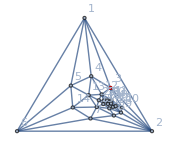

```mathematica
Graph[plantri[[10000]],VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{3}]
```

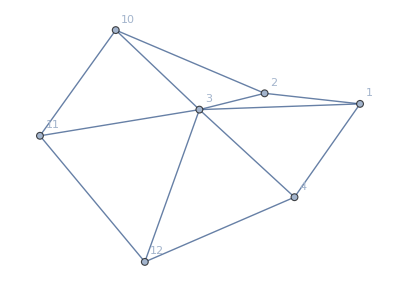

```mathematica
With[
{g=Graph[plantri[[10000]]]},
Graph[NeighborhoodGraph[g,3],VertexLabels->"Name"]
]
```

```mathematica
With[
{g=Graph[plantri[[10000]]]},
Table[{v->{VertexDegree[g,v],VertexList[NeighborhoodGraph[g,v]]}},{v,VertexList[g]}]
]
```

{{1→{5,{1,2,3,4,5,6}}},{2→{7,{2,1,3,6,7,8,9,10}}},{3→{6,{3,1,2,4,10,11,12}}},{4→{5,{4,1,3,5,12,13}}},{5→{5,{5,1,4,6,13,14}}},{6→{5,{6,1,2,5,7,14}}},{7→{5,{7,2,6,8,14,15}}},{8→{5,{8,2,7,9,15,16}}},{9→{6,{9,2,8,10,16,17,18}}},{10→{5,{10,2,3,9,11,18}}},{11→{6,{11,3,10,12,18,19,20}}},{12→{7,{12,3,4,11,13,20,21,22}}},{13→{6,{13,4,5,12,14,15,22}}},{14→{5,{14,5,6,7,13,15}}},{15→{7,{15,7,8,13,14,16,22,23}}},{16→{6,{16,8,9,15,17,23,24}}},{17→{5,{17,9,16,18,19,24}}},{18→{5,{18,9,10,11,17,19}}},{19→{5,{19,11,17,18,20,24}}},{20→{5,{20,11,12,19,21,24}}},{21→{5,{21,12,20,22,23,24}}},{22→{5,{22,12,13,15,21,23}}},{23→{5,{23,15,16,21,22,24}}},{24→{6,{24,16,17,19,20,21,23}}}}